```mathematica
xi1:=Sqrt[2]/2
```

```mathematica
xi1
```

1/(√2)

```mathematica
xi1:=-Sqrt[2]/2
```

```mathematica
xi2:=Sqrt[2]/2
```

```mathematica
xi1
```

-1/(√2)

```mathematica
xi2
```

1/(√2)

```mathematica
x1:=0
x2:=1/4
```

```mathematica
map[x_]:=x1*(1/2)*(a-x)+(x2/2)*(1+x)
```

```mathematica
map[1]
```

1/4

```mathematica
map[0]
```

1/8

```mathematica
map[-1]
```

0

```mathematica
map[xi1]
```

1/8 (1-1/(√2))

```mathematica
map[xi2]
```

1/8 (1+1/(√2))

```mathematica
c1:=map[xi1]
```

```mathematica
c2:=map[xi2]
```

```mathematica
c1
```

1/8 (1-1/(√2))

```mathematica
c2
```

1/8 (1+1/(√2))

```mathematica
f[x_]=Sqrt[1+x]
```

√(1+x)

```mathematica
y[x_]=f[c1]*(x-x2)/(x1-x2)+f[c2]*(x-x1)/(x2-x1)
```

-4 √(1+1/8 (1-1/(√2))) (-1/4+x)+4 √(1+1/8 (1+1/(√2))) x

```mathematica
y[x_]=f[c1]*(x-c2)/(c1-c2)+f[c2]*(x-c1)/(c2-c1)
```

(√(1+1/8 (1-1/(√2))) (1/8 (-1-1/(√2))+x))/(1/8 (-1-1/(√2))+1/8 (1-1/(√2)))+(√(1+1/8 (1+1/(√2))) (1/8 (-1+1/(√2))+x))/(1/8 (-1+1/(√2))+1/8 (1+1/(√2)))

```mathematica
Simplify[y[x]]
```

```mathematica
(√(36-2 √(y[x]2))+2 √(18-√2)-2 √(18+√2)+√(2 (18+√2))-16 (√(18-√2)-√(18+√2)) x)/(8 √2)
```

1/(8 √2)(2 √(18-√2)-2 √(18+√2)+√(2 (18+√2))-16 (√(18-√2)-√(18+√2)) x+√(36-2 √2 √((√(1+1/8 (1-1/(√2))) (1/8 (-1-1/(√2))+x))/(1/8 (-1-1/(√2))+1/8 (1-1/(√2)))+(√(1+1/8 (1+1/(√2))) (1/8 (-1+1/(√2))+x))/(1/8 (-1+1/(√2))+1/8 (1+1/(√2))))))

```mathematica
y[x]
```

(√(1+1/8 (1-1/(√2))) (1/8 (-1-1/(√2))+x))/(1/8 (-1-1/(√2))+1/8 (1-1/(√2)))+(√(1+1/8 (1+1/(√2))) (1/8 (-1+1/(√2))+x))/(1/8 (-1+1/(√2))+1/8 (1+1/(√2)))

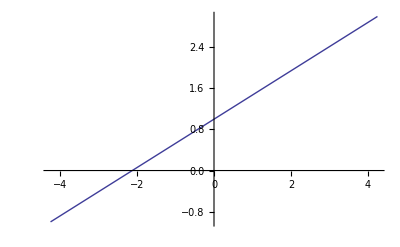

```mathematica
Plot[(√(1+1/8 (1-1/(√2))) (1/8 (-1-1/(√2))+x))/(1/8 (-1-1/(√2))+1/8 (1-1/(√2)))+(√(1+1/8 (1+1/(√2))) (1/8 (-1+1/(√2))+x))/(1/8 (-1+1/(√2))+1/8 (1+1/(√2))),{x,-4.243044805615793,4.243044805615793}]
```

```mathematica
f[x]
```

√(1+x)

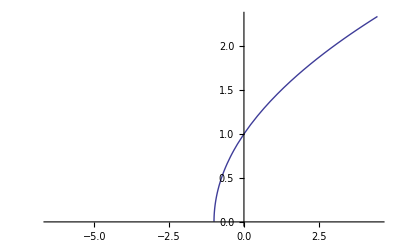

```mathematica
Plot[√(1+x),{x,-6.46,4.46}]
```

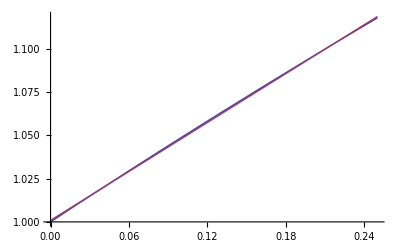

```mathematica
Plot[{f[x],y[x]},{x,0,1/4}]
```

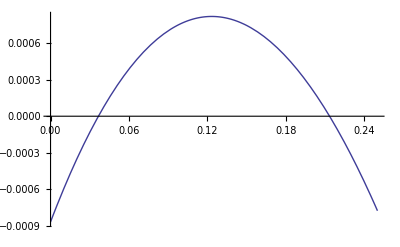

```mathematica
Plot[f[x]-y[x],{x,0,1/4}]
```

```mathematica
y[x_]:=f[c1]*(x-c2)/(c1-c2)+f[c2]*(x-c1)/(c2-c1)
```

```mathematica
y[x]
```

(√(1+1/8 (1-1/(√2))) (1/8 (-1-1/(√2))+x))/(1/8 (-1-1/(√2))+1/8 (1-1/(√2)))+(√(1+1/8 (1+1/(√2))) (1/8 (-1+1/(√2))+x))/(1/8 (-1+1/(√2))+1/8 (1+1/(√2)))

```mathematica
y[x_]:=f[c1]*(x-x2)/(x1-x2)+f[c2]*(x-x1)/(x2-x1)
```

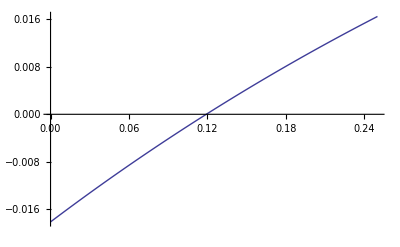

```mathematica
Plot[f[x]-y[x],{x,0,1/4}]
```

```mathematica
y[x_]:=f[c1]*(x-c2)/(c1-c2)+f[c2]*(x-c1)/(c2-c1)
```

```mathematica
Simplify[y[x]]
```

(√(36-2 √2)+2 √(18-√2)-2 √(18+√2)+√(2 (18+√2))-16 (√(18-√2)-√(18+√2)) x)/(8 √2)

```mathematica
(√(36-2 √2)+2 √(18-√2)-2 √(18+√2)+√(2 (18+√2))-16 (√(18-√2)-√(18+√2)) x)/(8 √2)
```

(√(36-2 √2)+2 √(18-√2)-2 √(18+√2)+√(2 (18+√2))-16 (√(18-√2)-√(18+√2)) x)/(8 √2)

```mathematica
√(36-2 √2)+2 √(18-√2)-2 √(18+√2)
```

√(36-2 √2)+2 √(18-√2)-2 √(18+√2)

```mathematica
N[√(36-2 √2)+2 √(18-√2)-2 √(18+√2)]
```

5.09229

```mathematica
√(2 (18+√2))-16 (√(18-√2)-√(18+√2)
```

```mathematica
√(2 (18+√2))-16 (√(18-√2)-√(18+√2))
```

√(2 (18+√2))-16 (√(18-√2)-√(18+√2))

```mathematica
N[√(2 (18+√2))-16 (√(18-√2)-√(18+√2))]
```

11.5687

```mathematica
8 √2
```

8 √2

```mathematica
N[8 √2]
```

11.3137

```mathematica
y[x]
```

(√(1+1/8 (1-1/(√2))) (1/8 (-1-1/(√2))+x))/(1/8 (-1-1/(√2))+1/8 (1-1/(√2)))+(√(1+1/8 (1+1/(√2))) (1/8 (-1+1/(√2))+x))/(1/8 (-1+1/(√2))+1/8 (1+1/(√2)))

```mathematica
N[y[x]]
```

-5.75948 (-0.213388+x)+6.23125 (-0.0366117+x)

```mathematica
Simplify[N[y[x]]]
```

1.00087+0.471769 x